# Week-5 (Assignment 4)

## Parametric Equations

```mathematica
y=x^2
```

x^2

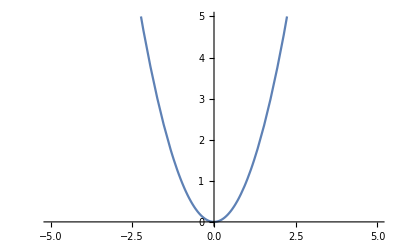

```mathematica
Plot[x^2,{x,-5,5},PlotRange->{0,5}]
```

say x=t. Then y=t^2
ParametricPlot[{t,t^2},{t,-5,5},PlotRange→{{-5,5},{0,5}}]

Set::write: Tag Times in t^4 t.Then is Protected.

Set::write: Tag Times in say t^2 is Protected.

t^2

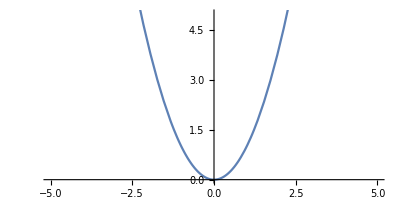

```mathematica
we have to graph the curve  x=y^4-3 y^2
```

-3 (-3 t^2+t^4)^4+(-3 t^2+t^4)^8

Set::write: Tag Times in curve graph have t^2 the to we is Protected.

```mathematica
Solve[x==y^4-3 y^2,y,Reals]
```

Solve::ivar: (-3 t^2+t^4)^2 is not a valid variable.

Solve[True,(-3 t^2+t^4)^2,ℝ]

```mathematica
Let y=t, Then x=t^4-3 t^2
```

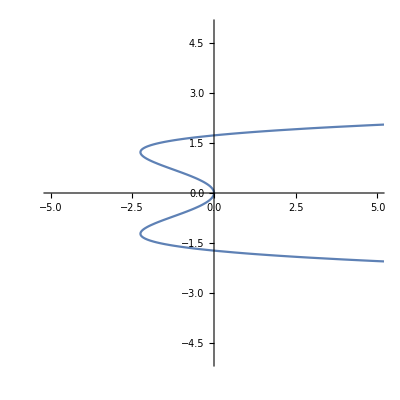

Set::write: Tag Times in (-3 t^2+t^4) t.Then is Protected.

Set::write: Tag Times in Let (-3 t^2+t^4)^2 is Protected.

-3 t^2+t^4

Set::write: Tag Times in curve graph have (-3 t^2+t^4) the to we is Protected.

{{}}

Set::write: Tag Times in curve graph have (-3 t^2+t^4) the to we is Protected.

```mathematica
ParametricPlot[{t^4-3 t^2,t},{t,-5,5},PlotRange->{-5,5}]
```

Find the area enclosed by the curve x=t^3+1, y=2t-t^2 and the x axis.

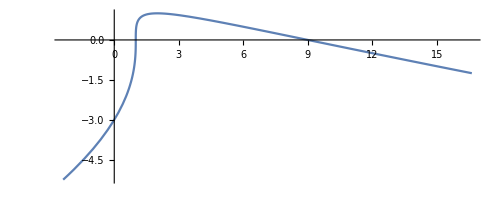

```mathematica
ParametricPlot[{t^3+1,2t-t^2},{t,-1.5,2.5}]
```

Say,x=f(t)=t^2+1 and y=g(t)=2t-t^2.
Area=∫_a^b yⅆx
ⅆx/ⅆt=3 t^2 = > dx=3 t^2 dt

```mathematica
Solve[2t-t^2==0,t,Reals]
```

{{t→0},{t→2}}

```mathematica
Area=∫_0^2 (2t-t^2)(3 t^2)ⅆt
```

Set::wrsym: Symbol Area is Protected.

24/5

Find the length of the curve x=t^2+1,y=2t-t^2  from t=0 to t=2.

L=∫_a^b √((ⅆx/ⅆt)^2+(ⅆy/ⅆt)^2)ⅆt

Integrate::diffbody: Unmatched differential operator ⅆt found in the integrand body of ∫_a^b √((ⅆx/ⅆt)^2+(ⅆy/ⅆt)^2)ⅆt. There may be too many differential operators or they may not appear at the end of the integral.

```mathematica
D[t^3+1,t]
```

3 t^2

```mathematica
D=[2t=t^2,t]
```

```mathematica
L=∫_0^2 √((3 t^2)^2+(2-2t)^2)ⅆt//N
```

8.7891

Parametric equations of a semicircle are x=r cos(t) and y=r sin(t). Rotate the semicircle about x-axis and find the area of the surface.
about x axis.
S=∫_a^b 2Pi yⅆs where ds=√((ⅆx/ⅆt)^2+(ⅆy/ⅆt)^2)

```mathematica
∫_0^Pi 2Pi r Sin[t] √(r^3(-Sin[t])^2+r^3(Cos[t])^2)ⅆt
```

4 π r √(r^3)

```mathematica
Graph r=3Sin[2θ]  for 0≤θ ≤ 2π.
```

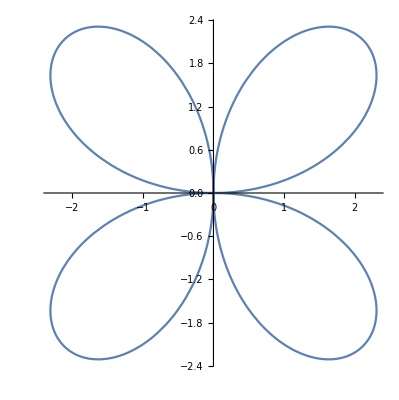

```mathematica
PolarPlot[3Sin[2θ],{θ,0, 2π}]
```

The path of the particle is given by:
x=sin(t)
y=2Sin[t]
z=cos(t)
Plot the path of the particle for 0 ≤ t ≤ 2π

```mathematica
ParametricPlot3D[{Sin[t],2Sin[t],Cos[t]},{t,0,2π},PlotRange->{{-2,2},{-2,2},{-2,2}}]
```

-Graphics3D-

```mathematica
x=4Sin[ϕ]Cos[θ ]
```

4 Cos[θ] Sin[ϕ]

```mathematica
y=3Sin[ϕ] Sin[θ ]
```

3 Sin[θ] Sin[ϕ]

```mathematica
z=2Cos[ϕ]
```

2 Cos[ϕ]

```mathematica
ParametricPlot3D[{x,y,z},{θ ,0,π},{ϕ,0,2π},ColorFunction->"Rainbow",Background->LightBlue,Axes->False,Boxed->False]
```

-Graphics3D-

Positions of two particles at time t are given by:
x1 = Sin[t], y1 = t
x2 = Cos[t], y2 = π/4 - t

Do their paths intersect? Do they collide too?

```mathematica
ClearAll["Global *"]
```

```mathematica
a=ParametricPlot[{Sin[t],t},{t,0,π},ColorFunction-> "Rainbow"];
```

```mathematica
b=ParametricPlot[{Cos[t] t,π/4-t},{t,0,π}];
```

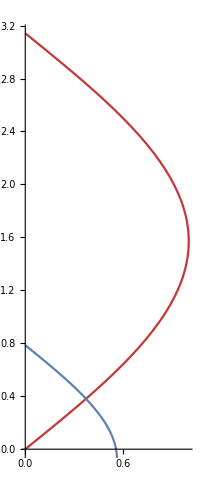

```mathematica
Show[a,b]
```

```mathematica
Solve[{Sin[t]==Cos[2t]&&0≤ t≤ π,t==π/3-t},t,Reals]
```

{{t→π/6}}

A quantum particle has the initial wave function:

Ψ (x,0)=Piecewise[{{Sin[πx/a]^3, 0≤ x≤ a/2}, {(5a)/6-x, a/2≤ x≤ (5a)/6}}]

1)Use the normalizing condition∫_0^a (Ψ(x,0))^2 ⅆx=1 to find A.
2) Graph Ψ(x,0) for a=3.

```mathematica
ClearAll["Global`*"]
```

```mathematica
ψ[x_]=Piecewise[{{Sin[π x/a]^3,0≤ x≤ a/2},{(5a)/6-x,a/2≤ x≤ (5a)/6}}]
```

Piecewise[{{Sin[(π x)/a]^3, 0≤x≤a/2}, {(5 a)/6-x, a/2≤x≤(5 a)/6}, {0, True}}]

```mathematica
∫_0^(a/2) (A Sin[(π x)/a]^3)^2 ⅆx+∫_(a/2)^a (A((5a)/6-x))^2 ⅆx
```

(5 a A^2)/32+(a^3 A^2)/72

```mathematica
Solve[(5 a A^2)/32+(a^3 A^2)/72==1,A,Reals]
```

{{A→ConditionalExpression[-12 √2 √(1/(45 a+4 a^3)), a>0]},{A→ConditionalExpression[12 √2 √(1/(45 a+4 a^3)), a>0]}}

```mathematica
a=3;
```

```mathematica
A=12 √2 √(1/(45 a+4 a^3));
```

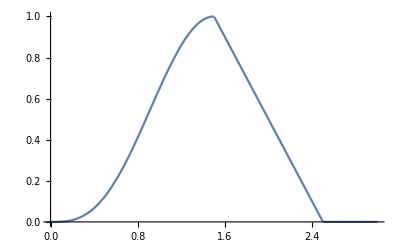

```mathematica
Plot[ψ[x],{x,0,a}]
```